```mathematica
Quit
```

{InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x],InterpolatingFunction[…][x]}

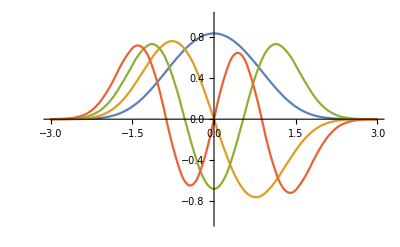

{1.39243,4.64966,8.65912,13.1696}

```mathematica
k0 = 1;k1=1;
v[x_]:=k0 x^2+k1 x^4; (*Potential*)
Plot[v[x],{x,-1,1}];

LL=3;(*x range and boundary parameter*)
{vals,funcs}=NDEigensystem[-ψ''[x] + v[x]ψ[x],{ψ[x]},{x,-LL,LL},4];
plotTab = Table[funcs[[a]],{a,1,Length[funcs]}]
Plot[plotTab,{x,-LL,LL},PlotRange->{{-LL,LL},{-1,1}}]
vals
```